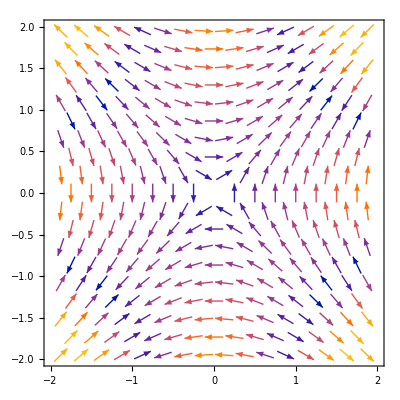

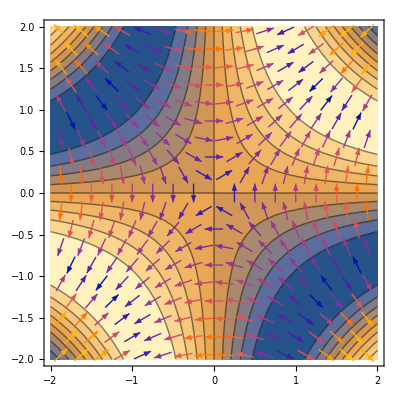

```mathematica
f[x_,y_]:=Sin[x*y]
VectorPlot[Evaluate@Grad[f[x,y],{x,y}],{x,-2,2},{y,-2,2}]
Show[ContourPlot[f[x,y],{x,-2,2},{y,-2,2}],%]
```